```mathematica
KnotTheoryPath = "~/projects/KnotTheory/trunk/";
AppendTo[$Path, KnotTheoryPath];
<< KnotTheory`
```

Loading KnotTheory` version of March 22, 2011, 21:10:4.67737.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
PD[Knot[3,1]]
```

PD[X[1,4,2,5],X[3,6,4,1],X[5,2,6,3]]

```mathematica
threeTwistIdentity=1/v Twist^3-(w^2/v-1+v/w^2)Twist^2-(w^2/v-v+v/w^2)Twist+v -v^18(bracket[λ]bracket[λ-1]brace[6])/brace[2] CupCap+v^9 bracket[1]Iweb
```

Twist^3/v+v+Iweb v^9 (-1/v+v)-(CupCap v^18 (1/v^6+v^6) (-1/w+w) (-v/w+w/v))/(1/v^2+v^2)-Twist^2 (-1+v/w^2+w^2/v)-Twist (-v+v/w^2+w^2/v)

```mathematica
bracket[(a_Integer:1) λ+(b_Integer:0)]:=w^a v^b-w^-a v^-b
brace[(a_Integer:1) λ+(b_Integer:0)]:=w^a v^b+w^-a v^-b
bracket[(b_Integer:0)]:=v^b-v^-b
brace[(b_Integer:0)]:=v^b+v^-b
```

```mathematica
CupCap/:Twist^(k_.) CupCap:=(v^12)^k CupCap
Iweb/:Twist^(k_.) Iweb:=(-v^6)^k Iweb
```

```mathematica
id1=Collect[Expand[threeTwistIdentity Twist^-1],Twist|CupCap|Iweb,Together]
```

Twist^2/v+v/Twist+Iweb (v^2-v^4)+(Twist (-v^2+v w^2-w^4))/(v w^2)+(-v^2+v^2 w^2-w^4)/(v w^2)+(CupCap v (-v^2+v^6-v^10+w^2+v^2 w^2-v^4 w^2-v^6 w^2+v^8 w^2+v^10 w^2-w^4+v^4 w^4-v^8 w^4))/w^2

```mathematica
id2=Collect[Expand[threeTwistIdentity Twist^-2],Twist|CupCap|Iweb,Together]
```

Twist/v+v/Twist^2+(Iweb (-1+v^2))/v^4+(-v^2+v w^2-w^4)/(v w^2)+(-v^2+v^2 w^2-w^4)/(Twist v w^2)+(CupCap (-v^2+v^6-v^10+w^2+v^2 w^2-v^4 w^2-v^6 w^2+v^8 w^2+v^10 w^2-w^4+v^4 w^4-v^8 w^4))/(v^11 w^2)

```mathematica
tangleIdentity=Collect[id1/Coefficient[id1,Iweb]-id2/Coefficient[id2,Iweb],Twist|CupCap,Together]
```

-Twist^2/(v^3 (-1+v^2))-v^5/(Twist^2 (-1+v^2))+(Twist (v^2-v w^2-v^6 w^2+w^4))/(v^3 (-1+v^2) w^2)+(v^6-w^2-v^6 w^2+v^4 w^4)/(Twist v (-1+v^2) w^2)+(v^2+v^8-v^2 w^2-v^7 w^2+w^4+v^6 w^4)/(v^3 (-1+v^2) w^2)-(CupCap (1+v^6) (-v^2+v^6-v^10+w^2+v^2 w^2-v^4 w^2-v^6 w^2+v^8 w^2+v^10 w^2-w^4+v^4 w^4-v^8 w^4))/(v^7 (-1+v^2) w^2)

```mathematica
-Collect[tangleIdentity/Coefficient[tangleIdentity,Twist^2]-Twist^2,Twist|CupCap,Together]
```

-v^8/Twist^2-(Twist (-v^2+v w^2+v^6 w^2-w^4))/w^2-(v^2 (-v^6+w^2+v^6 w^2-v^4 w^4))/(Twist w^2)-(-v^2-v^8+v^2 w^2+v^7 w^2-w^4-v^6 w^4)/w^2-(CupCap (1+v^6) (-v^2+v^6-v^10+w^2+v^2 w^2-v^4 w^2-v^6 w^2+v^8 w^2+v^10 w^2-w^4+v^4 w^4-v^8 w^4))/(v^4 w^2)

```mathematica
claspRule=NegativeClasp[a_,b_,c_,d_,{e_,f_}]:>{uX[d,a,e,f]uX[f,e,b,c],uX[a,b,c,d],P[a,b]P[d,c],uX[d,a,b,c],P[a,d]P[b,c]}.{-v^8,-(-v^2+v w^2+v^6 w^2-w^4)/w^2,-(v^2 (-v^6+w^2+v^6 w^2-v^4 w^4))/w^2,-(-v^2-v^8+v^2 w^2+v^7 w^2-w^4-v^6 w^4)/w^2,-((1+v^6) (-v^2+v^6-v^10+w^2+v^2 w^2-v^4 w^2-v^6 w^2+v^8 w^2+v^10 w^2-w^4+v^4 w^4-v^8 w^4))/(v^4 w^2)};
```

```mathematica
undoClaspRule={NegativeClasp[a_,b_,c_,d_,{e_,f_}]:>uX[a,e,f,d]uX[e,b,c,f]};
```

```mathematica
uX[a_,a_,b_,c_]:=v^-12 P[b,c]
uX[a_,b_,b_,c_]:=v^12 P[a,c]
uX[a_,b_,c_,c_]:=v^-12 P[b,c]
uX[a_,b_,c_,a_]:=v^12 P[b,c]
```

```mathematica
P/:uX[a_,b_,c_,d_]P[a_,e_]:=uX[e,b,c,d]
P/:uX[a_,b_,c_,d_]P[b_,e_]:=uX[a,e,c,d]
P/:uX[a_,b_,c_,d_]P[c_,e_]:=uX[a,b,e,d]
P/:uX[a_,b_,c_,d_]P[d_,e_]:=uX[a,b,c,e]
```

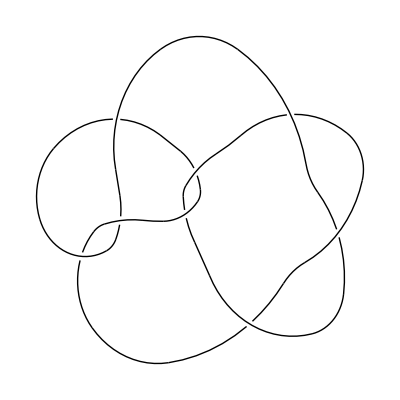

```mathematica
DrawPD[Knot[8,19]]
```

```mathematica
FindClasps[diagram:HoldPattern[Times[___uX]]]:=Module[{XX,claspDiagram,clasps},
XX/:XX[a_,b_,c_,d_]XX[b_,e_,f_,c_]:=NegativeClasp[a,e,f,d,{b,c}];
XX/:XX[a_,b_,c_,d_]XX[d_,c_,e_,f_]:=PositiveClasp[a,b,e,f,{c,d}];
claspDiagram=diagram/.uX->XX;
clasps=Cases[claspDiagram,_NegativeClasp|_PositiveClasp];
{#,DeleteCases[claspDiagram,#]/.undoClaspRule/.XX->uX}&/@clasps
]
```

```mathematica
pd=Times@@PD[Knot[8,19]]/.X->uX
```

uX[2,8,3,7] uX[4,2,5,1] uX[5,13,6,12] uX[8,4,9,3] uX[9,15,10,14] uX[11,1,12,16] uX[13,7,14,6] uX[15,11,16,10]

```mathematica
FindClasps[pd]
```

{{NegativeClasp[2,4,9,7,{8,3}],uX[4,2,5,1] uX[5,13,6,12] uX[9,15,10,14] uX[11,1,12,16] uX[13,7,14,6] uX[15,11,16,10]},{NegativeClasp[5,7,14,12,{13,6}],uX[2,8,3,7] uX[4,2,5,1] uX[8,4,9,3] uX[9,15,10,14] uX[11,1,12,16] uX[15,11,16,10]},{NegativeClasp[9,11,16,14,{15,10}],uX[2,8,3,7] uX[4,2,5,1] uX[5,13,6,12] uX[8,4,9,3] uX[11,1,12,16] uX[13,7,14,6]}}

```mathematica
Clear[QuantumExceptionalInvariant]
QuantumExceptionalInvariant[diagram:HoldPattern[Times[___uX]]]:=QuantumExceptionalInvariant[diagram]=Module[{clasps=FindClasps[diagram]},
If[clasps==={},
Print["No clasp in ",diagram];
$Failed,
CollectDiagrams[Expand[(#⟦1⟧/.claspRule)(#⟦2⟧)],QuantumExceptionalInvariant]&@clasps⟦1⟧
]
]
```

```mathematica
CollectDiagrams[diagrams_,f_:(#&)]:=Module[{constant,arrays,Xs},
Xs=Union[Cases[diagrams,_uX,∞]];
If[Xs==={},diagrams,
arrays=CoefficientArrays[diagrams,Xs];
constant=arrays⟦1⟧;
arrays=Rest[arrays];
constant+Plus@@Cases[Flatten[ArrayRules/@arrays],(i:{__Integer}->c_):>f[Times@@Xs⟦i⟧]c]
]
]
```

```mathematica
QuantumExceptionalInvariant[pd]
```

No clasp in uX[6,11,15,10] uX[15,11,6,10]

No clasp in uX[11,15,10,6] uX[15,11,6,10]

No clasp in uX[11,13,10,16] uX[13,11,16,10]

No clasp in uX[6,13,15,10] uX[15,13,6,10]

No clasp in uX[6,13,15,10] uX[10,15,13,6]

No clasp in uX[11,15,10,16] uX[15,11,16,10]

No clasp in uX[15,11,16,10] uX[16,11,15,10]

No clasp in uX[10,15,11,16] uX[16,11,13,6]

No clasp in uX[13,11,16,6] uX[16,11,13,6]

No clasp in uX[6,13,11,16] uX[16,11,13,6]

No clasp in uX[15,11,16,10] uX[16,11,13,6]

No clasp in uX[6,13,15,10] uX[15,11,16,10]

No clasp in uX[13,15,10,6] uX[15,11,16,10]

No clasp in uX[11,1,12,16] uX[11,16,12,1]

No clasp in uX[9,1,12,14] uX[9,14,12,1]

No clasp in uX[9,14,12,1] uX[14,9,1,12]

No clasp in uX[9,14,12,1] uX[11,1,12,16] uX[14,9,11,16]

No clasp in uX[9,14,12,1] uX[11,1,12,16]

No clasp in uX[5,7,14,1] uX[14,7,5,1]

No clasp in uX[5,7,16,12] uX[11,1,12,16] uX[11,7,5,1]

No clasp in uX[5,7,14,12] uX[9,7,5,1] uX[11,1,12,16] uX[14,9,11,16]

No clasp in uX[5,7,14,12] uX[9,1,12,14] uX[9,7,5,1]

No clasp in uX[5,7,14,12] uX[14,7,5,12]

No clasp in uX[5,7,14,12] uX[12,14,7,5]

No clasp in uX[5,7,14,12] uX[9,7,5,1]

No clasp in uX[5,7,14,12] uX[9,7,5,1] uX[11,1,12,16]

No clasp in uX[1,5,7,14] uX[14,7,5,1]

No clasp in uX[11,1,12,14] uX[11,7,5,1] uX[12,5,7,14]

No clasp in uX[9,7,5,1] uX[11,1,12,16] uX[12,5,7,14] uX[14,9,11,16]

No clasp in uX[9,1,12,14] uX[9,7,5,1] uX[12,5,7,14]

No clasp in uX[12,5,7,14] uX[14,7,5,12]

No clasp in uX[12,5,7,14] uX[12,14,7,5]

No clasp in uX[9,7,5,1] uX[12,5,7,14]

No clasp in uX[9,7,5,1] uX[11,1,12,16] uX[12,5,7,14]

No clasp in uX[11,1,12,14] uX[11,7,5,1]

No clasp in uX[9,7,5,1] uX[11,1,12,16] uX[14,9,11,16]

No clasp in uX[9,1,12,14] uX[9,7,5,1]

No clasp in uX[9,7,5,1] uX[14,9,1,12]

No clasp in uX[9,7,5,1] uX[11,1,12,16]

No clasp in uX[9,11,16,14] uX[11,1,14,16]

No clasp in uX[11,1,14,16] uX[14,9,11,16]

No clasp in uX[2,4,9,16] uX[4,2,12,1] uX[9,1,12,16]

No clasp in uX[4,2,12,1] uX[11,1,12,16]

No clasp in uX[2,4,1,14] uX[4,2,14,1]

No clasp in uX[2,4,9,14] uX[4,2,12,1] uX[9,1,12,14]

No clasp in uX[4,2,12,1] uX[16,11,1,12]

No clasp in uX[4,2,12,1] uX[10,15,11,16] uX[11,1,12,16]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[9,1,12,14] uX[12,5,7,14]

No clasp in uX[2,4,1,7] uX[4,2,7,1]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[12,5,7,14] uX[14,9,1,12]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[12,5,7,14]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[11,1,12,16] uX[12,5,7,14] uX[14,9,11,16]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[11,1,12,16] uX[12,5,7,14]

No clasp in uX[2,4,14,7] uX[4,2,5,12] uX[5,7,14,12]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[5,7,16,12] uX[9,1,12,16]

No clasp in uX[2,4,1,12] uX[4,2,5,1]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[5,7,14,12] uX[14,9,1,12]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[5,7,14,12] uX[9,1,12,14]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[5,7,14,12]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[5,7,14,12] uX[11,1,12,16] uX[14,9,11,16]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[5,7,14,12] uX[11,1,12,16]

No clasp in uX[2,4,14,7] uX[4,2,5,12]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[9,1,12,14]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[11,1,12,16] uX[14,9,11,16]

No clasp in uX[2,4,1,7] uX[4,2,5,1]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[14,9,1,12]

No clasp in uX[2,4,9,7] uX[4,2,5,1]

No clasp in uX[2,4,9,7] uX[4,2,5,1] uX[11,1,12,16]

No clasp in uX[4,2,5,9] uX[5,2,4,9]

No clasp in uX[4,2,5,16] uX[5,2,4,9]

No clasp in uX[4,2,5,14] uX[5,2,4,9]

No clasp in uX[4,2,5,1] uX[5,2,4,9]

No clasp in uX[4,2,5,1] uX[5,2,4,9] uX[11,1,14,16] uX[14,9,11,16]

No clasp in uX[4,2,5,1] uX[5,2,4,9] uX[11,1,14,16]

No clasp in uX[4,2,12,1] uX[9,1,12,16] uX[16,2,4,9]

No clasp in uX[4,2,12,1] uX[11,1,12,16] uX[14,2,4,9] uX[14,9,11,16]

No clasp in uX[4,2,12,9] uX[12,2,4,9]

No clasp in uX[4,2,12,1] uX[9,1,12,14] uX[14,2,4,9]

No clasp in uX[4,2,12,1] uX[14,2,4,9] uX[14,9,1,12]

No clasp in uX[4,2,12,1] uX[14,2,4,9]

No clasp in uX[4,2,12,1] uX[11,1,12,16] uX[14,2,4,9]

No clasp in uX[4,2,5,1] uX[7,2,4,9] uX[9,1,12,14] uX[12,5,7,14]

No clasp in uX[4,2,5,1] uX[7,2,4,9] uX[12,5,7,14] uX[14,9,1,12]

No clasp in uX[4,2,5,1] uX[7,2,4,9] uX[12,5,7,14]

No clasp in uX[4,2,5,1] uX[7,2,4,9] uX[11,1,12,16] uX[12,5,7,14] uX[14,9,11,16]

No clasp in uX[4,2,5,1] uX[7,2,4,9] uX[11,1,12,16] uX[12,5,7,14]

No clasp in uX[4,2,5,12] uX[12,5,2,4]

No clasp in uX[4,2,5,12] uX[5,2,4,12]

No clasp in uX[4,2,5,1] uX[5,7,16,12] uX[7,2,4,9] uX[9,1,12,16]

No clasp in uX[4,2,5,9] uX[12,2,4,9]

No clasp in uX[4,2,5,1] uX[5,7,14,12] uX[7,2,4,9] uX[14,9,1,12]

No clasp in uX[4,2,5,1] uX[5,7,14,12] uX[7,2,4,9] uX[9,1,12,14]

No clasp in uX[4,2,5,1] uX[5,7,14,12] uX[7,2,4,9]

No clasp in uX[4,2,5,1] uX[5,7,14,12] uX[7,2,4,9] uX[11,1,12,16] uX[14,9,11,16]

No clasp in uX[4,2,5,1] uX[5,7,14,12] uX[7,2,4,9] uX[11,1,12,16]

No clasp in uX[4,2,5,12] uX[7,2,4,14]

No clasp in uX[4,2,5,1] uX[7,2,4,9] uX[9,1,12,14]

No clasp in uX[4,2,5,1] uX[7,2,4,9] uX[11,1,12,16] uX[14,9,11,16]

No clasp in uX[4,2,5,9] uX[7,2,4,9]

No clasp in uX[4,2,5,1] uX[7,2,4,9] uX[14,9,1,12]

No clasp in uX[4,2,5,1] uX[7,2,4,9]

No clasp in uX[4,2,5,1] uX[7,2,4,9] uX[11,1,12,16]

No clasp in uX[4,2,7,1] uX[11,1,14,16] uX[14,9,11,16]

No clasp in uX[4,2,7,1] uX[11,1,14,16]

No clasp in uX[4,2,12,1] uX[9,1,12,7]

No clasp in uX[4,2,12,1] uX[7,9,1,12]

No clasp in uX[4,2,12,1] uX[7,9,11,16] uX[11,1,12,16]

No clasp in uX[1,5,7,9] uX[4,2,5,1]

No clasp in uX[4,2,5,1] uX[9,1,12,14] uX[12,5,7,14]

No clasp in uX[4,2,5,1] uX[11,1,12,16] uX[12,5,7,14] uX[14,9,11,16]

No clasp in uX[4,2,5,1] uX[12,5,7,14] uX[14,9,1,12]

No clasp in uX[4,2,5,1] uX[12,5,7,14]

No clasp in uX[4,2,5,1] uX[11,1,12,16] uX[12,5,7,14]

No clasp in uX[4,2,5,12] uX[5,7,9,12]

No clasp in uX[4,2,5,1] uX[5,7,16,12] uX[9,1,12,16]

No clasp in uX[4,2,5,1] uX[5,7,14,12] uX[11,1,12,16] uX[14,9,11,16]

No clasp in uX[4,2,5,1] uX[5,7,14,12] uX[14,9,1,12]

No clasp in uX[4,2,5,1] uX[5,7,14,12] uX[9,1,12,14]

No clasp in uX[4,2,5,1] uX[5,7,14,12]

No clasp in uX[4,2,5,1] uX[5,7,14,12] uX[11,1,12,16]

No clasp in uX[4,2,5,1] uX[9,1,12,14]

No clasp in uX[4,2,5,1] uX[11,1,12,16] uX[14,9,11,16]

No clasp in uX[4,2,5,1] uX[14,9,1,12]

No clasp in uX[4,2,5,1] uX[11,1,12,16]

-v^8 («5»+(PositiveClasp[7,2,4,9,{8,3}]-PositiveClasp[7,2,4,9,{8,3}]/v^4-PositiveClasp[7,2,4,9,{8,3}]/v^2-2 v^4 PositiveClasp[7,2,4,9,{8,3}]+«17»+v^4 w^2 PositiveClasp[7,2,4,9,{8,3}]-v^6 w^2 PositiveClasp[7,2,4,9,{8,3}]+v^10 w^2 PositiveClasp[7,2,4,9,{8,3}]) («1»+«32»))+«3»+(-1/v^10-1/v^4+1/(v^4 w^2)+w^2/v^6) (-v^32 P[11,16]^2-v^34 P[11,16]^2+«27»+(-v^2-v^7+v^2/w^2+v^8/w^2+w^2+v^6 w^2) ((-v^2-v^8+v^8/w^2+v^6 w^2) $Failed+«30»+«1»+(-v-v^6+v^2/w^2+w^2) («1»))+(-v-v^6+v^2/w^2+w^2) («32»+(-v^2-v^7+v^2/w^2+v^8/w^2+w^2+v^6 w^2) ((-v-v^6+v^2/w^2+w^2) $Failed+(-v^2-v^7+v^2/w^2+v^8/w^2+w^2+v^6 w^2) $Failed-P[10,15]^2-P[10,15]^2/v^16-P[10,15]^2/v^14+P[10,15]^2/v^12-(2 P[10,15]^2)/v^8+P[10,15]^2/v^4-P[10,15]^2/v^2+P[10,15]^2/w^2+P[10,15]^2/(v^14 w^2)-P[10,15]^2/(v^10 w^2)+P[10,15]^2/(v^8 w^2)+P[10,15]^2/(v^6 w^2)-P[10,15]^2/(v^4 w^2)+(w^2 P[10,15]^2)/v^16-(w^2 P[10,15]^2)/v^12+(w^2 P[10,15]^2)/v^10+(w^2 P[10,15]^2)/v^8-(w^2 P[10,15]^2)/v^6+(w^2 P[10,15]^2)/v^2-v^14 P[13,15]^2-v^20 P[13,15]^2+(v^20 P[13,15]^2)/w^2+v^18 w^2 P[13,15]^2-v^8 PositiveClasp[6,13,11,16,{15,10}] QuantumExceptionalInvariant[uX[16,11,13,6]])))